```mathematica
SetOptions[EvaluationNotebook[],CellContext->Notebook];SetDirectory[NotebookDirectory[]];
```

```mathematica
(* Calculate mass, radius, moment of inertia, and tidal Love number in GR *)
```

## 1. Equations

```mathematica
n=4;coord={t,r,th,ph};arg1=coord[[2]];
```

```mathematica
repa2m={af[arg1]->(1-(2*mf[arg1])/arg1)^-1,af'[arg1]->D[(1-(2*mf[arg1])/arg1)^-1,arg1],af''[arg1]->D[(1-(2*mf[arg1])/arg1)^-1,arg1,arg1]}//Simplify;
```

```mathematica
(* background equations *)
```

```mathematica
bgeqset=<<"nrpolytrop_GR_bgeqs.txt";
```

```mathematica
(* even perturbation equations *)
```

```mathematica
perteqset=<<"nrpolytrop_GR_eveneqs.txt";
```

```mathematica
AbsoluteTiming[bgeqset1=bgeqset/.repa2m//Simplify;perteqset1=perteqset/.repa2m//Simplify;{bpsol,mpsol,ppsol}={bf'[r],mf'[r],pf'[r]}/.Solve[{bgeqset1[[1]]==0,bgeqset1[[2]]==0,bgeqset1[[3]]==0},{bf'[r],mf'[r],pf'[r]}][[1]]];
```

```mathematica
soleh2=eh2f[r]/.Solve[perteqset1[[6]]==0,eh2f[r]][[1]];perteqset2=Simplify[perteqset1/.{si->0}/.l->2/.{eh1f[r]->0,eh1f'[r]->0,eh1f''[r]->0,eh2f[r]->soleh2,eh2f'[r]->D[soleh2,r],eh2f''[r]->D[soleh2,r,r]}/.{bf'[r]->bpsol,bf''[r]->D[bpsol,r],mf'[r]->mpsol,mf''[r]->D[mpsol,r],pf'[r]->ppsol,pf''[r]->D[ppsol,r]}];
```

```mathematica
testsol2d=Solve[{perteqset2[[1]]==0,perteqset2[[7]]==0,perteqset2[[9]]==0},{eh0f''[r],ekf''[r],w1f''[r]}];perteqset3=Simplify[perteqset2/.testsol2d[[1]]];testsol1d=Solve[{perteqset3[[3]]==0,perteqset3[[5]]==0,perteqset3[[10]]==0},{eh0f'[r],ekf'[r],w1f'[r]}];{eh0psol,ekpsol,w1psol}={eh0f'[r],ekf'[r],w1f'[r]}/.testsol1d[[1]];perteqset4=perteqset3/.testsol1d[[1]]//Simplify;
```

```mathematica
testeqset={eh0psol,ekpsol}/.{pf[r]->0,epf[r]->0,mf[r]->bm};{testeh0sol,testeksol}={eh0f[r],ekf[r]}/.DSolve[{testeqset[[1]]==eh0f'[r],testeqset[[2]]==ekf'[r]},{eh0f[r],ekf[r]},r][[1]];testsol=Solve[{testeh0sol==eh0,testeksol==ek},{C[1],C[2]}];tidalla=1/3*((2 C[2])/(5 bm))/C[1]/.testsol[[1]]//Simplify;
```

```mathematica
ek12ek=ekf[r]/r^2;eh012eh0=eh0f[r]/r^2;chvarrep={ekf[r]->r^2*ek1f[r],ekf'[r]->D[r^2*ek1f[r],r],eh0f[r]->r^2*eh01f[r],eh0f'[r]->D[r^2*eh01f[r],r]};
```

```mathematica
perteqset31={bf'[r]-bpsol,mf'[r]-mpsol,pf'[r]-ppsol,eh0f'[r]-eh0psol,ekf'[r]-ekpsol};perteqset32={bf'[r]-bpsol,mf'[r]-mpsol,pf'[r]-ppsol,eh0f'[r]-eh0psol,ekf'[r]-ekpsol}/.chvarrep//Simplify;
```

```mathematica
(* odd perturbation equations *)
```

```mathematica
pertoeqset=<<"nrpolytrop_GR_oddeqs.txt";
```

```mathematica
AbsoluteTiming[bgeqset1=bgeqset/.repa2m//Simplify;pertoeqset1=pertoeqset/.repa2m//Simplify;{bpsol,mpsol,ppsol}={bf'[r],mf'[r],pf'[r]}/.Solve[{bgeqset1[[1]]==0,bgeqset1[[2]]==0,bgeqset1[[3]]==0},{bf'[r],mf'[r],pf'[r]}][[1]]];
```

```mathematica
pertoeqset2=pertoeqset1/.{uf[r]->(bom*r^2)/(-1/2*Sqrt[3/Pi]*I*si)}/.l->1/.{oh1f[r]->0,oh1f'[r]->0}/.{bf''[r]->D[bpsol,r],mf''[r]->D[mpsol,r],pf''[r]->D[ppsol,r]}/.{bf'[r]->bpsol,mf'[r]->mpsol,pf'[r]->ppsol}//Simplify;pertoeqset3=pertoeqset2/.si->0;
```

```mathematica
reph02om={oh0f[r]->(omf[r]-bom)*r^2/(-1/2*Sqrt[3/Pi]),oh0f'[r]->D[(omf[r]-bom)*r^2/(-1/2*Sqrt[3/Pi]),r],oh0f''[r]->D[(omf[r]-bom)*r^2/(-1/2*Sqrt[3/Pi]),r,r]};perteqom=pertoeqset3[[1]]/.reph02om//Simplify;
```

```mathematica
(* parametrization *)
```

```mathematica
r2x=x*l0;parrep=Simplify[{bf[r]->bf[x],bf'[r]->D[bf[x],x]/D[r2x,x],bf''[r]->D[D[bf[x],x]/D[r2x,x],x]/D[r2x,x],mf[r]->l0*mf[x],mf'[r]->D[l0*mf[x],x]/D[r2x,x],mf''[r]->D[D[l0*mf[x],x]/D[r2x,x],x]/D[r2x,x],pf[r]->pf[x]/(ka/2*l0^2),pf'[r]->D[pf[x]/(ka/2*l0^2),x]/D[r2x,x],pf''[r]->D[D[pf[x]/(ka/2*l0^2),x]/D[r2x,x],x]/D[r2x,x],epf[r]->epf[x]/(ka/2*l0^2),epf'[r]->D[epf[x]/(ka/2*l0^2),x]/D[r2x,x],epf''[r]->D[D[epf[x]/(ka/2*l0^2),x]/D[r2x,x],x]/D[r2x,x],omf[r]->omf[x]/l0,omf'[r]->D[omf[x]/l0,x]/D[r2x,x],omf''[r]->D[D[omf[x]/l0,x]/D[r2x,x],x]/D[r2x,x],eh0f[r]->eh0f[x],eh0f'[r]->D[eh0f[x],x]/D[r2x,x],eh0f''[r]->D[D[eh0f[x],x]/D[r2x,x],x]/D[r2x,x],ekf[r]->ekf[x],ekf'[r]->D[ekf[x],x]/D[r2x,x],ekf''[r]->D[D[ekf[x],x]/D[r2x,x],x]/D[r2x,x],eh01f[r]->eh01f[x]/l0^2,eh01f'[r]->D[eh01f[x]/l0^2,x]/D[r2x,x],eh01f''[r]->D[D[eh01f[x]/l0^2,x]/D[r2x,x],x]/D[r2x,x],ek1f[r]->ek1f[x]/l0^2,ek1f'[r]->D[ek1f[x]/l0^2,x]/D[r2x,x],ek1f''[r]->D[D[ek1f[x]/l0^2,x]/D[r2x,x],x]/D[r2x,x],bm->l0*dimlbm}];
```

```mathematica
dimleqset=perteqset31/.parrep/.r->r2x//Simplify;dimlperteqom=perteqom/.parrep/.r->r2x//Simplify;dimleqsol={bf'[x],mf'[x],pf'[x],eh0f'[x],ekf'[x],omf''[x]}/.Solve[{dimleqset[[1]]==0,dimleqset[[2]]==0,dimleqset[[3]]==0,dimleqset[[4]]==0,dimleqset[[5]]==0,dimlperteqom==0},{bf'[x],mf'[x],pf'[x],eh0f'[x],ekf'[x],omf''[x]}][[1]]//Simplify;
```

```mathematica
dimleqset32=perteqset32/.parrep/.r->r2x//Simplify;dimleqsol32={bf'[x],mf'[x],pf'[x],eh01f'[x],ek1f'[x],omf''[x]}/.Solve[{dimleqset32[[1]]==0,dimleqset32[[2]]==0,dimleqset32[[3]]==0,dimleqset32[[4]]==0,dimleqset32[[5]]==0,dimlperteqom==0},{bf'[x],mf'[x],pf'[x],eh01f'[x],ek1f'[x],omf''[x]}][[1]]//Simplify;{eh012eh032,ek12ek32}={eh012eh0,ek12ek}/.parrep/.r->r2x//Simplify;tidalla32=tidalla/.parrep/.r->r2x//Simplify;
```

```mathematica
yset={bf[x],mf[x],pf[x],eh0f[x],ekf[x],omf[x],ompf[x]};ypset=D[yset,x];ypeqset={dimleqsol[[1]],dimleqsol[[2]],dimleqsol[[3]],dimleqsol[[4]],dimleqsol[[5]],ompf[x],dimleqsol[[6]]}/.{omf'[x]->ompf[x]};
```

```mathematica
(* polytropic EOS *)
```

```mathematica
ep2p=al*(pf[x])^bcon
```

al pf[x]^bcon

```mathematica
(* initial condition at the center *)
```

```mathematica
iterel={m3->(al p0^bcon)/3,p2->1/6 (-3 p0^2-al^2 p0^(2 bcon)-4 al p0^(1+bcon)),bb2->1/3 bb0 (3 p0+al p0^bcon),om2->2/5 om0 (p0+al p0^bcon),m5->-1/30 al bcon p0^(-1+bcon) (3 p0^2+al^2 p0^(2 bcon)+4 al p0^(1+bcon)),m7->1/2520 al bcon p0^(-2+bcon) (3 p0^2+al^2 p0^(2 bcon)+4 al p0^(1+bcon)) (15 (1+bcon) p0^2+al^2 (-5+13 bcon) p0^(2 bcon)+2 al (-10+19 bcon) p0^(1+bcon)),om4->1/(210 p0)om0 (p0+al p0^bcon) (3 p0^2-5 al^2 bcon p0^(2 bcon)+33 al p0^(1+bcon)-15 al bcon p0^(1+bcon)),bb4->(bb0 (5 p0-al bcon p0^bcon) (3 p0^2+al^2 p0^(2 bcon)+4 al p0^(1+bcon)))/(60 p0),p4->1/(180 p0)(3 p0^2+al^2 p0^(2 bcon)+4 al p0^(1+bcon)) (15 p0^2+4 al^2 bcon p0^(2 bcon)+9 al bcon p0^(1+bcon)),bb6->1/7560 al bb0 p0^(-2+bcon) (3 p0^2+al^2 p0^(2 bcon)+4 al p0^(1+bcon)) (3 (70-51 bcon+5 bcon^2) p0^2+al^2 bcon (-5+13 bcon) p0^(2 bcon)+2 al bcon (-59+19 bcon) p0^(1+bcon)),p6->-1/(22680 p0^2)(p0+al p0^bcon) (3 p0+al p0^bcon) (945 p0^4+al^4 bcon (-25+86 bcon) p0^(4 bcon)+36 al bcon (19+5 bcon) p0^(3+bcon)+3 al^2 (35-27 bcon+198 bcon^2) p0^(2+2 bcon)+10 al^3 bcon (-23+43 bcon) p0^(1+3 bcon)),h00->0,k0->0,k2->h02,k4->-(h02 (4 p0^2+al^2 bcon p0^(2 bcon)+al (-2+bcon) p0^(1+bcon)))/(14 p0),k6->1/(1512 p0^2)h02 (180 p0^4+al^4 bcon (-7+17 bcon) p0^(4 bcon)+3 al (-10+5 bcon+7 bcon^2) p0^(3+bcon)+al^2 (110-53 bcon+73 bcon^2) p0^(2+2 bcon)+3 al^3 bcon (-25+23 bcon) p0^(1+3 bcon)),h04->-(h02 (33 p0^2+3 al^2 bcon p0^(2 bcon)+al (1+3 bcon) p0^(1+bcon)))/(42 p0),h06->1/(7560 p0^2)h02 (4140 p0^4+5 al^4 bcon (-7+17 bcon) p0^(4 bcon)+3 al (190+169 bcon+35 bcon^2) p0^(3+bcon)+al^2 (430+311 bcon+365 bcon^2) p0^(2+2 bcon)+3 al^3 bcon (-77+115 bcon) p0^(1+3 bcon))};inib=bb0+bb2*x^2;inim=m3*x^3+m5*x^5;inip=p0+p2*x^2;iniom=om0+om2*x^2+om4*x^4;inih0=h02*x^2+h04*x^4;inik=k2*x^2+k4*x^4;
```

## 2. Input parameters

```mathematica
(* input polytropic index: 0<=n<=5 *)
```

```mathematica
npolyind=1.5;
```

## 3. Numerical solutions

```mathematica
pgnum1=9;pgnum2=15;pgnum3=22;pgnum4=32;
```

```mathematica
npt=200;{p0min,p0max}={0.00001,10000};p0set=Table[Exp[Log[p0min]+(Log[p0max]-Log[p0min])*(i-1)/(npt-1)],{i,1,npt}];resset=Table[0,{i,1,npt},{k,1,5}];
```

```mathematica
AbsoluteTiming[bconnum=npolyind/(npolyind+1);xini=0.0001;xinfrate=200;bgn=3;Do[ypeqsetnum=ypeqset/.epf[x]->ep2p/.{ka->8*Pi,l0->1,al->1,bcon->bconnum};ypeqsetnum1=ypeqsetnum;yset1=yset;ypset1=D[yset1,x];iniset={inib,inim,inip,inih0,inik,iniom,D[iniom,x]}/.iterel/.{ka->8*Pi,l0->1,al->1,bcon->bconnum}/.{bb0->1,h02->1,om0->1,p0->p0set[[testip]]}/.x->xini;iniset1=iniset;ndsoleqset=Table[ypeqsetnum1[[i]]==ypset1[[i]],{i,1,bgn}];ndsoliniset=Table[yset1[[i]]==iniset1[[i]],{i,1,bgn}]/.x->xini;ndsolyset={bf,mf,pf};sol=NDSolve[{ndsoleqset,ndsoliniset,WhenEvent[pf[x]<=iniset[[3]]*10^-pgnum2,"StopIntegration"]},ndsolyset,{x,xini,1000},MaxSteps->100000,Method->"ImplicitRungeKutta",InterpolationOrder->All,WorkingPrecision->pgnum3];testf=bf/.sol[[1]];{xnum1,xnum2}=testf["Domain"][[1]];test1=Re[yset1/.sol[[1]]/.x->xnum2];iniset1={bf[x],mf[x]}/.sol[[1]]/.x->xnum2;ypeqsetnum=ypeqset/.{epf[x]->0,pf[x]->0}/.{ka->8*Pi,l0->1,al->1,bcon->bconnum};ypeqsetnum1=ypeqsetnum;ndsoleqset=Table[ypeqsetnum1[[i]]==ypset1[[i]],{i,1,bgn-1}];ndsoliniset=Table[yset1[[i]]==iniset1[[i]],{i,1,bgn-1}]/.x->xnum2;ndsolyset={bf,mf};solext=NDSolve[{ndsoleqset,ndsoliniset},ndsolyset,{x,xnum2,xinfrate*xnum2},PrecisionGoal->pgnum3,InterpolationOrder->All,WorkingPrecision->pgnum3];mfsolnum=Re[Piecewise[{{mf[x]/.sol[[1]],x<=xnum2},{mf[x]/.solext[[1]],x>xnum2}}]];pfsolnum=Re[Piecewise[{{pf[x]/.sol[[1]],x<=xnum2},{0,x>xnum2}}]];ypeqsetnum1=Table[ypeqset[[i]],{i,bgn+1,Length[yset]}]/.epf[x]->ep2p/.{pf[x]->pfsolnum,mf[x]->mfsolnum}/.{ka->8*Pi,l0->1,al->1,bcon->bconnum};yset1=Table[yset[[i]],{i,bgn+1,Length[yset]}];ypset1=D[yset1,x];iniset1={inih0,inik,iniom,D[iniom,x]}/.iterel/.{ka->8*Pi,l0->1,al->1,bcon->bconnum}/.{bb0->1,h02->1,om0->1,p0->p0set[[testip]]}/.x->xini;ndsoleqset=Table[ypeqsetnum1[[i]]==ypset1[[i]],{i,1,Length[ypset1]}];ndsoliniset=Table[yset1[[i]]==iniset1[[i]],{i,1,Length[ypset1]}]/.x->xini;ndsolyset={eh0f,ekf,omf,ompf};soltidal=NDSolve[{ndsoleqset,ndsoliniset},ndsolyset,{x,xini,xinfrate*xnum2},PrecisionGoal->pgnum3,InterpolationOrder->All,WorkingPrecision->pgnum3];testj=x^4/6*ompf[x]/.sol[[1]]/.soltidal[[1]]/.x->xnum2;testbom=omf[x]+x/3*ompf[x]/.sol[[1]]/.soltidal[[1]]/.x->xnum2;resset[[testip,3]]=testj/testbom;resset[[testip,1]]=xnum2;resset[[testip,2]]=Re[mf[x]/.sol[[1]]/.x->xnum2];resset[[testip,4]]=Re[tidalla32/.{eh0->eh0f[x],ek->ekf[x]}/.soltidal[[1]]/.x->xnum2/.{l0->1,dimlbm->resset[[testip,2]]}],{testip,1,npt}]]
```

NDSolve::precw: The precision of the differential equation ({{(2 bf[x] (mf[x]+x^3 pf[x]))/(x (x-2 mf[«1»]))==bf'[x],x^2 pf[x]^0.6==mf'[x],-((pf[x]^(«19»)+pf[x]) (mf[x]+x^3 pf[x]))/(x (x-2 mf[«1»]))==pf'[x],bf[0.0001]==1.,mf[0.0001]==3.33333×10^-16,pf[0.0001]==0.00001},{},{},{},{«1»}}) is less than WorkingPrecision (22.).

NDSolve::impsitsf: Unable to satisfy the ImplicitSolver tolerance for IterationSafetyFactor at x = 17.85802008105351388579.

NDSolve::impsitsf: Unable to satisfy the ImplicitSolver tolerance for IterationSafetyFactor at x = 17.85870939289518340997.

NDSolve::nrnum1: The function value -1.963039826956982678866×10^-17-8.615635867198977142124×10^-21 ⅈ is not a real number when the arguments are {17.85750644528770398997,1.051008951901196066553-4.070549119915069530012×10^-22 ⅈ,0.3158146509514013410406-2.676417939564327278758×10^-15 ⅈ,1.964039826956809548323×10^-17+8.615635867198977511817×10^-21 ⅈ}.

NDSolve::impsitsf: Unable to satisfy the ImplicitSolver tolerance for IterationSafetyFactor at x = 17.85902898331599931072.

General::stop: Further output of NDSolve::impsitsf will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(2 x ekf[x] (x+Times[«2»])+eh0f[x] (Times[«2»]+Times[«2»]+Times[«3»]+Times[«3»]+Times[«3»]+Times[«4»]+Times[«2»]))/(x (x-2 Re[«1»]) (Power[«2»] Re[«1»]+Re[Piecewise[«2»]]))==eh0f'[x],«6»,ompf[0.0001]==8.08×10^-8},{},{},{},{}}) is less than WorkingPrecision (22.).

NDSolve::precw: The precision of the differential equation ({{(2 bf[x] (mf[x]+x^3 pf[x]))/(x (x-2 mf[«1»]))==bf'[x],x^2 pf[x]^0.6==mf'[x],-((pf[x]^(«19»)+pf[x]) (mf[x]+x^3 pf[x]))/(x (x-2 mf[«1»]))==pf'[x],bf[0.0001]==1.,mf[0.0001]==3.54825×10^-16,pf[0.0001]==0.0000110975},«3»,{WhenEvent[«1»]}}) is less than WorkingPrecision (22.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::nrnum1: The function value 1.917891801690725331391×10^-19-8.408677197005644917933×10^-20 ⅈ is not a real number when the arguments are {17.65636619810123560383,1.053224963522536765982-9.5474418054931548732×10^-21 ⅈ,0.3248675610912778619913-2.423152811793864200691×10^-14 ⅈ,-1.806916552069197019101×10^-19+8.408677197005645372788×10^-20 ⅈ}.

NDSolve::nrnum1: The function value -3.289255010860069346002×10^-17-6.073251378369675845552×10^-21 ⅈ is not a real number when the arguments are {17.45579859049755398981,1.055536773952660708158-2.864088089838678135506×10^-22 ⅈ,0.3341395150433583285447-1.623157670741174883226×10^-15 ⅈ,3.290486561463138307264×10^-17+6.073251378369675893756×10^-21 ⅈ}.

General::stop: Further output of NDSolve::nrnum1 will be suppressed during this calculation.

NDSolve::maxit: Maximum number of iterations 44 reached at x = 12.07937359030970253472.

NDSolve::maxit: Maximum number of iterations 44 reached at x = 11.12030316141545028892.

NDSolve::maxit: Maximum number of iterations 44 reached at x = 10.96363307787438789194.

General::stop: Further output of NDSolve::maxit will be suppressed during this calculation.

NDSolve::mxst: Maximum number of 10000 steps reached at the point x == 8.348420991383473002001.

InterpolatingFunction::dmval: Input value {8.414943911524382496555} lies outside the range of data in the interpolating function. Extrapolation will be used.

Power::infy: Infinite expression 1/(0``-12.2845455365433) encountered.

Power::infy: Infinite expression 1/(0``-12.585575532207281) encountered.

Infinity::indet: Indeterminate expression 0``-24.843016803012297 ComplexInfinity ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0``-12.558471266462664 ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0``-14.056418948396413 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NDSolve::nlnum: The function value {Indeterminate,Indeterminate,62.20634010188699939617,Indeterminate} is not a list of numbers with dimensions {4} at {x,eh0f[x],ekf[x],omf[x],ompf[x]} = {8.414943911524382496555,7.905820687540132593831,9.243641943758746799915,34232.46165141886881354,62.20634010188699939617}.

NDSolve::mxst: Maximum number of 10000 steps reached at the point x == 8.125085782615840242674.

InterpolatingFunction::dmval: Input value {8.181358771536462666785} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::mxst: Maximum number of 10000 steps reached at the point x == 7.931030338219904877867.

General::stop: Further output of NDSolve::mxst will be suppressed during this calculation.

Power::infy: Infinite expression 1/(0``-0.03057457926046978) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NDSolve::nlnum: The function value {Indeterminate,ComplexInfinity,145.2024021494726552301,-81.06932816053047977643} is not a list of numbers with dimensions {4} at {x,eh0f[x],ekf[x],omf[x],ompf[x]} = {7.676096784467957670053,5.364619452388281383196,6.369720778728558795083,55172.57591316696674506,145.2024021494726552301}.

{220.941,Null}

## 4. Plots

### 4.1 Mass-radius relation

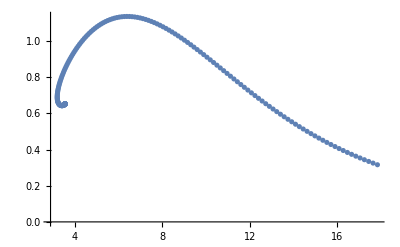

```mathematica
ListPlot[Table[{resset[[testip,1]],resset[[testip,2]]},{testip,1,npt}]]
```

### 4.2 Factor of Moment of inertia vs. mass

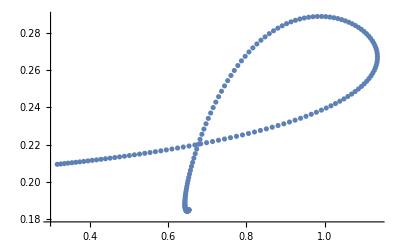

```mathematica
ListPlot[Table[{resset[[testip,2]],resset[[testip,3]]/(resset[[testip,2]]*(resset[[testip,1]])^2)},{testip,1,npt}]]
```

### 4.3 Tidal Love number vs. mass

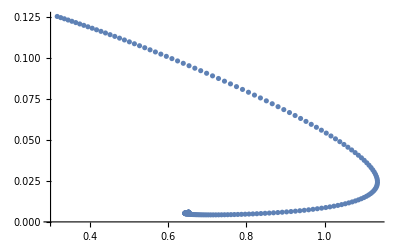

```mathematica
ListPlot[Table[{resset[[i,2]],3/2*resset[[i,4]]/(resset[[i,1]])^5},{i,1,npt}]]
```